### functions

```mathematica
matrixPower[matrix_,power_]:=Module[{evsTransposed=Transpose[Eigenvectors[matrix]],eas=Eigenvalues[matrix]+1.*^-9},
Return[evsTransposed.DiagonalMatrix[eas^power].Inverse[evsTransposed]]]
overlapSimilarity[cov1_,cov2_]:=Module[{sqrtCov1=matrixPower[cov1,1/2],sqrtCov2=matrixPower[cov2,1/2]},Return[Tr[sqrtCov1.sqrtCov2]/Norm[sqrtCov1,"Frobenius"]/Norm[sqrtCov2,"Frobenius"]]]
```

```mathematica
covGeneration[eas_,evs_]:=Module[{evsNormalized=ConstantArray[0.,Dimensions[evs]],evN=Length[evs]},Do[evsNormalized[[evIdx]]=Normalize[evs[[evIdx]]],{evIdx,evN}];Return[Transpose[evsNormalized].DiagonalMatrix[eas].evsNormalized]]
```

### demo

#### 1d data

```mathematica
plotN=8;covs=Table[{covGeneration[{1},{{1,0,0}}]+1.*^-9*IdentityMatrix[3],covGeneration[{1},{{Cos[angle],Sin[angle],0}}]+1*^-9*IdentityMatrix[3]},{angle,0,Pi,Pi/plotN}];
plots=Table[ListPointPlot3D[{RandomVariate[MultinormalDistribution[{0,0,0},covs[[angleIdx+1,1]]],500],RandomVariate[MultinormalDistribution[{0,0,0},covs[[angleIdx+1,2]]],500]},PlotRange->Table[{-4,4},3],AspectRatio->1],{angleIdx,0,plotN}];
quantifications=Table[{Cos[angleIdx*Pi/plotN],(Cos[angleIdx*Pi/plotN*2]+1)/2,overlapSimilarity[covs[[angleIdx+1,1]],covs[[angleIdx+1,2]]]},{angleIdx,0,plotN}]*1.;
methods={"Cos","(Cos+1)/2","overlapSimilarity"};
```

```mathematica
Grid[Transpose[ArrayFlatten[{{{{"plot"}},{methods}},{Transpose[{plots}],quantifications}}]],Frame->All]
```

plot | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
Cos | 1. | 0.92388 | 0.707107 | 0.382683 | 0. | -0.382683 | -0.707107 | -0.92388 | -1.
(Cos+1)/2 | 1. | 0.853553 | 0.5 | 0.146447 | 0. | 0.146447 | 0.5 | 0.853553 | 1.
overlapSimilarity | 1. | 0.853566 | 0.500045 | 0.146523 | 0.0000894447 | 0.146523 | 0.500045 | 0.853566 | 1.

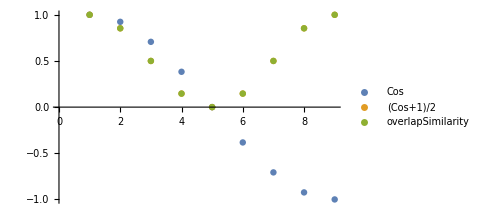

```mathematica
ListPlot[Transpose[quantifications],PlotLegends->methods,ImageSize->Medium]
```

#### 2d data one-axis-aligned

```mathematica
plotN=8;zVar=(*0.*)3;covs=Table[{covGeneration[{1,zVar},{{1,0,0},{0,0,1}}]+1.*^-9*IdentityMatrix[3],covGeneration[{1,zVar},{{Cos[phi],Sin[phi],0},{0,0,1}}]+1*^-9*IdentityMatrix[3]},{phi,0,Pi,Pi/plotN}];
plots=Table[ListPointPlot3D[{RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,1]]],500],RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,2]]],500]},PlotRange->Table[{-4,4},3],AspectRatio->1],{phiIdx,0,plotN}];
quantifications=Table[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,Total[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,1}*{1,Identity[zVar]}]/Total[{1,Identity[zVar]}],overlapSimilarity[covs[[phiIdx+1,1]],covs[[phiIdx+1,2]]]},{phiIdx,0,plotN}];
methods={"CosSimilarity:(Cos+1)/2","totVar^2WeightedCosSimilarity/totVar","overlapSimilarity"};
```

```mathematica
Grid[Transpose[ArrayFlatten[{{{{"plot"}},{methods}},{Transpose[{plots}],quantifications}}]],Frame->All]
```

plot | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
CosSimilarity:(Cos+1)/2 | 1. | 0.853553 | 0.5 | 0.146447 | 0. | 0.146447 | 0.5 | 0.853553 | 1.
totVar^2WeightedCosSimilarity/totVar | 1. | 0.963388 | 0.875 | 0.786612 | 0.75 | 0.786612 | 0.875 | 0.963388 | 1.
overlapSimilarity | 1. | 0.963392 | 0.875011 | 0.786631 | 0.750022 | 0.786631 | 0.875011 | 0.963392 | 1.

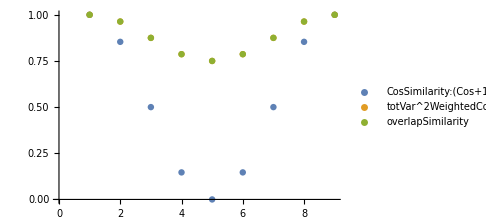

```mathematica
ListPlot[Transpose[quantifications],PlotLegends->methods,ImageSize->Medium]
```

#### 2d data rotate-by-r-hat

```mathematica
plotN=8;
zVar=(*0.*)3;
theta=Pi/6;
covs=Table[{covGeneration[{1,zVar},{{1,0,0},{0,0,1}}]+1.*^-9*IdentityMatrix[3],covGeneration[{1,zVar},{{Cos[phi],Sin[phi],0},{Sin[phi]Sin[theta],-Cos[phi]Sin[theta],Cos[theta]}}]+1*^-9*IdentityMatrix[3]},{phi,0,Pi,Pi/plotN}];
plots=Table[ListPointPlot3D[{RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,1]]],500],RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,2]]],500]},PlotRange->Table[{-4,4},3],AspectRatio->1],{phiIdx,0,plotN}];
quantifications=Table[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,Total[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,(Cos[theta*2]+1)/2*1.}*{1,Identity[zVar]}]/Total[{1,Identity[zVar]}],overlapSimilarity[covs[[phiIdx+1,1]],covs[[phiIdx+1,2]]]},{phiIdx,0,plotN}];
methods={"CosSimilarity:(Cos+1)/2","totVar^2WeightedCosSimilarity/totVar","overlapSimilarity"};
```

```mathematica
Grid[Transpose[ArrayFlatten[{{{{"plot"}},{methods}},{Transpose[{plots}],quantifications}}]],Frame->All]
```

plot | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
CosSimilarity:(Cos+1)/2 | 1. | 0.853553 | 0.5 | 0.146447 | 0. | 0.146447 | 0.5 | 0.853553 | 1.
totVar^2WeightedCosSimilarity/totVar | 0.8125 | 0.775888 | 0.6875 | 0.599112 | 0.5625 | 0.599112 | 0.6875 | 0.775888 | 0.8125
overlapSimilarity | 0.81251 | 0.791753 | 0.741644 | 0.691534 | 0.670778 | 0.691534 | 0.741644 | 0.791753 | 0.81251

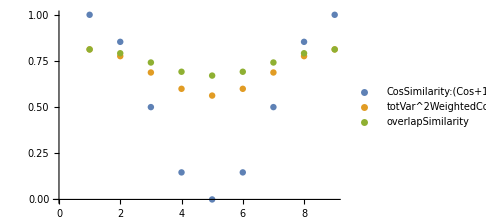

```mathematica
ListPlot[Transpose[quantifications],PlotLegends->methods,ImageSize->Medium]
```

#### 2d data rotate-by-phi-hat

```mathematica
plotN=8;
zVar=(*0.*)3;
theta=Pi/6;
covs=Table[{covGeneration[{1,zVar},{{1,0,0},{0,0,1}}]+1.*^-9*IdentityMatrix[3],covGeneration[{1,zVar},{{Cos[phi]Cos[theta],Sin[phi]Cos[theta],Sin[theta]},{Cos[phi]Sin[theta],Sin[phi]Sin[theta],Cos[theta]}}]+1*^-9*IdentityMatrix[3]},{phi,0,Pi,Pi/plotN}];
plots=Table[ListPointPlot3D[{RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,1]]],500],RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,2]]],500]},PlotRange->Table[{-4,4},3],AspectRatio->1],{phiIdx,0,plotN}];
quantifications=Table[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,Total[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,(Cos[theta*2]+1)/2*1.}*{1,Identity[zVar]}]/Total[{1,Identity[zVar]}],overlapSimilarity[covs[[phiIdx+1,1]],covs[[phiIdx+1,2]]]},{phiIdx,0,plotN}];
methods={"CosSimilarity:(Cos+1)/2","totVar^2WeightedCosSimilarity/totVar","overlapSimilarity"};
```

```mathematica
Grid[Transpose[ArrayFlatten[{{{{"plot"}},{methods}},{Transpose[{plots}],quantifications}}]],Frame->All]
```

plot | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
CosSimilarity:(Cos+1)/2 | 1. | 0.853553 | 0.5 | 0.146447 | 0. | 0.146447 | 0.5 | 0.853553 | 1.
totVar^2WeightedCosSimilarity/totVar | 0.8125 | 0.775888 | 0.6875 | 0.599112 | 0.5625 | 0.599112 | 0.6875 | 0.775888 | 0.8125
overlapSimilarity | 0.855845 | 0.819667 | 0.732325 | 0.644984 | 0.608806 | 0.644984 | 0.732325 | 0.819667 | 0.855845

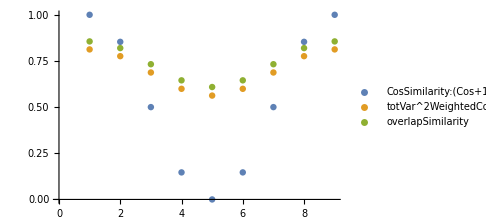

```mathematica
ListPlot[Transpose[quantifications],PlotLegends->methods,ImageSize->Medium]
```